```mathematica
corr51=corr512[[All,1]];
corr52=corr512[[All,2]];
corr101=corr1012[[All,1]];
corr102=corr1012[[All,2]];
corr201=corr2012[[All,1]];
corr202=corr2012[[All,2]];
corr301=corr3012[[All,1]];
corr302=corr3012[[All,2]];
corr401=corr4012[[All,1]];
corr402=corr4012[[All,2]];
corr501=corr5012[[All,1]];
corr502=corr5012[[All,2]];
corr1001=corr10012[[All,1]];
corr1002=corr10012[[All,2]];
```

```mathematica
j=24;
val=1000;
For[α=0,α≤2,α+=0.01,
l5k=Table[{corr51[[i]],Log[corr52[[i]]]-α*Log[5000]},{i,j,49}];
l50k=Table[{corr501[[i]],Log[corr502[[i]]]-α*Log[50000]},{i,j,49}];
l100k=Table[{corr1001[[i]],Log[corr1002[[i]]]-α*Log[100000]},{i,30,49}];
l10k=Table[{corr101[[i]],Log[corr102[[i]]]-α*Log[10000]},{i,j,49}];
l20k=Table[{corr201[[i]],Log[corr202[[i]]]-α*Log[20000]},{i,j,49}];
l30k=Table[{corr301[[i]],Log[corr302[[i]]]-α*Log[30000]},{i,j,49}];
l40k=Table[{corr401[[i]],Log[corr402[[i]]]-α*Log[40000]},{i,j,49}];
i5=Interpolation[l5k];
i10=Interpolation[l10k];
i20=Interpolation[l20k];
i30=Interpolation[l30k];
i40=Interpolation[l40k];
i50=Interpolation[l50k];
i100=Interpolation[l100k];
min=corr51[[j]];
max=corr51[[49]];
delta=(corr51[[49]]-corr51[[j]])/50.;
int=Sum[delta*(Max[i5[min+k*delta],i10[min+k*delta],i20[min+k*delta],i30[min+k*delta],i40[min+k*delta],i50[min+k*delta],i100[min+k*delta]]-Min[i5[min+k*delta],i10[min+k*delta],i20[min+k*delta],i30[min+k*delta],i40[min+k*delta],i50[min+k*delta],i100[min+k*delta]]),{k,0,50}];
If[int<val,
val=int;
αf=α;
]
]
" = val"  val
" = α" αf
```

0.00565001  = val

0.58  = α

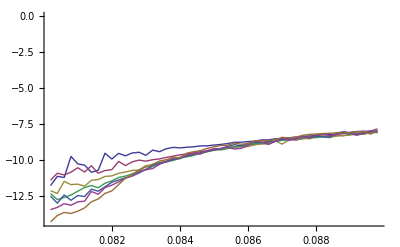

```mathematica
j=1;
α=0.59;
l5k=Table[{corr51[[i]],Log[corr52[[i]]]-α*Log[5000]},{i,j,49}];
l50k=Table[{corr501[[i]],Log[corr502[[i]]]-α*Log[50000]},{i,j,49}];
l100k=Table[{corr1001[[i]],Log[corr1002[[i]]]-α*Log[100000]},{i,j,49}];
l10k=Table[{corr101[[i]],Log[corr102[[i]]]-α*Log[10000]},{i,j,49}];
l20k=Table[{corr201[[i]],Log[corr202[[i]]]-α*Log[20000]},{i,j,49}];
l30k=Table[{corr301[[i]],Log[corr302[[i]]]-α*Log[30000]},{i,j,49}];
l40k=Table[{corr401[[i]],Log[corr402[[i]]]-α*Log[40000]},{i,j,49}];
ListLinePlot[{l5k,l10k,l20k,l30k,l40k,l50k,l100k}]
```